```mathematica
ClearAll["global`*"]
```

## Solution in external harmonic potential

```mathematica
M={{-(2*κ+k)/γ,0},{0,-k/γ}};
```

```mathematica
MatrixForm[M]
```

((-k-2 κ)/γ | 0
0 | -k/γ)

```mathematica
expM=MatrixExp[M*(t-tp)];
```

```mathematica
covar=Integrate[expM.{{4/γ^2*2*(Subscript[T, 1]+Subscript[T, 2])/2*γ/2,1/γ^2*2*(Subscript[T, 1]-Subscript[T, 2])*γ/2},{1/γ^2*2*(Subscript[T, 1]-Subscript[T, 2])*γ/2,1/(4*γ^2)*2*(Subscript[T, 1]+Subscript[T, 2])/2*2*γ}}.Transpose[expM],{tp,-Infinity,t},Assumptions->{γ>0,k>0,κ>0}];
```

```mathematica
P[R_,r_,kk_]:=Simplify[Exp[-1/2*{r,R}.Inverse[covar].{r,R}]]/.{k->kk}
```

## Patching and normalization

```mathematica
SubMinus[k]=2*Subscript[U, 0]/L^2;
```

```mathematica
SubPlus[k]=2*Subscript[U, 0]/l^2;
```

```mathematica
SubMinus[f]=Integrate[P[R,r,SubMinus[k]],{r,-Infinity,Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

```mathematica
SubPlus[f]=Integrate[P[R,r,SubPlus[k]],{r,-Infinity,Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

```mathematica
{{SubMinus[exprA],SubPlus[exprA]}}=Simplify[Solve[SubMinus[A]*(SubMinus[f]/.{R->0})==SubPlus[A]*(SubPlus[f]/.{R->0})&&SubMinus[A]*Integrate[SubMinus[f],{R,-L,0},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>Subscript[T, 2]>0}]+SubPlus[A]*Integrate[SubPlus[f],{R,0,l},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>Subscript[T, 2]>0}]==1,{SubMinus[A],SubPlus[A]}],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

## Current

```mathematica
Subscript[J, R]=Simplify[-k*R/γ*P[R,r,k]-(Subscript[T, 1]+Subscript[T, 2])/(4*γ)*D[P[R,r,k],R]-(Subscript[T, 1]-Subscript[T, 2])/(2*γ)*D[P[R,r,k],r]];
```

```mathematica
{{SubPlus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/P[R,r,k]/.{R->l,k->SubPlus[k]})==0,r],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Set::shape: Lists {{exprr_+}} and Solve[(8 P[l,r,2 Power[«2»] Subscript[«2»]] U_0+2 l (T_1-Subscript[«2»]) P^(0,1,0)[l,r,2 Power[«2»] Subscript[«2»]]+l (T_1+T_2) P^(1,0,0)[l,r,2 Power[«2»] Subscript[«2»]])/P[l,r,(2 U_0)/l^2]==0,r] are not the same shape.

Solve[(8 P[l,r,(2 U_0)/l^2] U_0+2 l (T_1-T_2) P^(0,1,0)[l,r,(2 U_0)/l^2]+l (T_1+T_2) P^(1,0,0)[l,r,(2 U_0)/l^2])/P[l,r,(2 U_0)/l^2]==0,r]

```mathematica
{{SubMinus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/P[R,r,k]/.{R->-L,k->SubMinus[k]})==0,r],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Set::shape: Lists {{exprr_-}} and Solve[(8 P[-L,r,2 Power[«2»] Subscript[«2»]] U_0+2 L (-Subscript[«2»]+T_2) P^(0,1,0)[-L,r,2 Power[«2»] Subscript[«2»]]-L (T_1+T_2) P^(1,0,0)[-L,r,2 Power[«2»] Subscript[«2»]])/P[-L,r,(2 U_0)/L^2]==0,r] are not the same shape.

Solve[(8 P[-L,r,(2 U_0)/L^2] U_0+2 L (-T_1+T_2) P^(0,1,0)[-L,r,(2 U_0)/L^2]-L (T_1+T_2) P^(1,0,0)[-L,r,(2 U_0)/L^2])/P[-L,r,(2 U_0)/L^2]==0,r]

```mathematica
Subscript[J, right]=Integrate[SubPlus[A]*Subscript[J, R]/.{R->l,k->SubPlus[k],SubPlus[exprA]},{r,r/.{SubPlus[exprr]},Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

```mathematica
Subscript[J, left]=Integrate[SubMinus[A]*Subscript[J, R]/.{R->-L,k->SubMinus[k],SubMinus[exprA]},{r,-Infinity,r/.{SubMinus[exprr]}},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

```mathematica
Subscript[J, total]=Simplify[Subscript[J, right]+Subscript[J, left],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}]
```

```mathematica
(2 ⅇ^(-(4 Subscript[U, 0])/(Subscript[T, 1]+Subscript[T, 2])) κ (Subscript[T, 1]-Subscript[T, 2]) (-L^3 κ √(Subscript[U, 0] (l^2 κ+Subscript[U, 0]) (l^4 κ^2 Subscript[T, 1]^2+l^4 κ^2 Subscript[T, 2]^2+2 Subscript[T, 1] Subscript[T, 2] (l^4 κ^2+8 l^2 κ Subscript[U, 0]+8 Subscript[U, 0]^2)))+l^3 κ √(Subscript[U, 0] (L^2 κ+Subscript[U, 0]) (L^4 κ^2 Subscript[T, 1]^2+L^4 κ^2 Subscript[T, 2]^2+2 Subscript[T, 1] Subscript[T, 2] (L^4 κ^2+8 L^2 κ Subscript[U, 0]+8 Subscript[U, 0]^2)))+Subscript[U, 0] (-L √(Subscript[U, 0] (l^2 κ+Subscript[U, 0]) (l^4 κ^2 Subscript[T, 1]^2+l^4 κ^2 Subscript[T, 2]^2+2 Subscript[T, 1] Subscript[T, 2] (l^4 κ^2+8 l^2 κ Subscript[U, 0]+8 Subscript[U, 0]^2)))+l √(Subscript[U, 0] (L^2 κ+Subscript[U, 0]) (L^4 κ^2 Subscript[T, 1]^2+L^4 κ^2 Subscript[T, 2]^2+2 Subscript[T, 1] Subscript[T, 2] (L^4 κ^2+8 L^2 κ Subscript[U, 0]+8 Subscript[U, 0]^2))))))/((l+L) π γ Erf[2 √(Subscript[U, 0]/(Subscript[T, 1]+Subscript[T, 2]))] √((l^2 κ+Subscript[U, 0]) (L^2 κ+Subscript[U, 0]) (l^4 κ^2 Subscript[T, 1]^2+l^4 κ^2 Subscript[T, 2]^2+2 Subscript[T, 1] Subscript[T, 2] (l^4 κ^2+8 l^2 κ Subscript[U, 0]+8 Subscript[U, 0]^2)) (L^4 κ^2 Subscript[T, 1]^2+L^4 κ^2 Subscript[T, 2]^2+2 Subscript[T, 1] Subscript[T, 2] (L^4 κ^2+8 L^2 κ Subscript[U, 0]+8 Subscript[U, 0]^2))))
```

(2 ⅇ^(-(4 U_0)/(T_1+T_2)) κ (T_1-T_2) (-L^3 κ √(U_0 (l^2 κ+U_0) (l^4 κ^2 T_1^2+l^4 κ^2 T_2^2+2 T_1 T_2 (l^4 κ^2+8 l^2 κ U_0+8 U_0^2)))+l^3 κ √(U_0 (L^2 κ+U_0) (L^4 κ^2 T_1^2+L^4 κ^2 T_2^2+2 T_1 T_2 (L^4 κ^2+8 L^2 κ U_0+8 U_0^2)))+U_0 (-L √(U_0 (l^2 κ+U_0) (l^4 κ^2 T_1^2+l^4 κ^2 T_2^2+2 T_1 T_2 (l^4 κ^2+8 l^2 κ U_0+8 U_0^2)))+l √(U_0 (L^2 κ+U_0) (L^4 κ^2 T_1^2+L^4 κ^2 T_2^2+2 T_1 T_2 (L^4 κ^2+8 L^2 κ U_0+8 U_0^2))))))/((l+L) π γ Erf[2 √(U_0/(T_1+T_2))] √((l^2 κ+U_0) (L^2 κ+U_0) (l^4 κ^2 T_1^2+l^4 κ^2 T_2^2+2 T_1 T_2 (l^4 κ^2+8 l^2 κ U_0+8 U_0^2)) (L^4 κ^2 T_1^2+L^4 κ^2 T_2^2+2 T_1 T_2 (L^4 κ^2+8 L^2 κ U_0+8 U_0^2))))

```mathematica
Subscript[J, total]= (2 ⅇ^(-(4 Subscript[U, 0])/(Subscript[T, 1]+Subscript[T, 2])) κ (Subscript[T, 1]-Subscript[T, 2]) (l √((Subscript[U, 0] (l^2 κ+Subscript[U, 0]))/(l^4 κ^2 (Subscript[T, 1]+Subscript[T, 2])^2+16 l^2 κ Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]+16 Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]^2))-L √((Subscript[U, 0] (L^2 κ+Subscript[U, 0]))/(L^4 κ^2 (Subscript[T, 1]+Subscript[T, 2])^2+16 L^2 κ Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]+16 Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]^2))))/((l+L) π γ Erf[2 √(Subscript[U, 0]/(Subscript[T, 1]+Subscript[T, 2]))]);
```

```mathematica
Subscript[J, unitless]=Simplify[ Subscript[J, total]/.{Subscript[T, 1]->Subscript[T, 1]*Subscript[U, 0],Subscript[T, 2]->Subscript[T, 2]*Subscript[U, 0],L->Subscript[λ, l]*d,l->Subscript[λ, r]*d,κ->κ*Subscript[U, 0]/d^2},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0}];
```

```mathematica
Subscript[J, paper]= Simplify[Subscript[J, unitless]/.{Subscript[T, 1]->T*(1-δ),Subscript[T, 2]->T*(1+δ)},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,T>0,Abs[δ]<1,d>0}];
```

```mathematica
forplot = FullSimplify[Subscript[J, unitless]/(Subscript[U, 0]/(γ*d))/.{d->1,Subscript[λ, r]->1-Subscript[λ, l],γ->1},{κ>0,Subscript[λ, l]>0,Subscript[T, 1]>0,Subscript[T, 2]>0,Subscript[U, 0]>0}];
```

## Expansion in strong spring

```mathematica
Subscript[J, exp]= Subscript[J, paper]/.{κ->q*T}
```

(2 ⅇ^(-2/T) q T δ U_0 (λ_l √((1+q T λ_l^2)/(4-4 δ^2-4 q T (-1+δ^2) λ_l^2+q^2 T^2 λ_l^4))-λ_r √((1+q T λ_r^2)/(4-4 δ^2-4 q T (-1+δ^2) λ_r^2+q^2 T^2 λ_r^4))))/(d^2 π γ Erf[(√2)/(√T)] (λ_l+λ_r))

```mathematica
FullSimplify[Subscript[J, exp],{q>0,Subscript[λ, l]>0,Subscript[λ, r]>0,Subscript[T, 1]>0,Subscript[T, 2]>0,Abs[δ]<1,Subscript[U, 0]>0,Abs[δ]<1}]
```

(2 ⅇ^(-2/T) q T δ U_0 (λ_l √((1+q T λ_l^2)/(4-4 δ^2+q T λ_l^2 (4-4 δ^2+q T λ_l^2)))-λ_r √((1+q T λ_r^2)/(4-4 δ^2+q T λ_r^2 (4-4 δ^2+q T λ_r^2)))))/(d^2 π γ Erf[(√2)/(√T)] (λ_l+λ_r))

```mathematica
FullSimplify[Series[Subscript[J, exp],{q,∞,0}],{q>0,Subscript[λ, l]>0,Subscript[λ, r]>0,Subscript[T, 1]>0,Subscript[T, 2]>0,Abs[δ]<1,Subscript[U, 0]>0,Abs[δ]<1}]
```

-(ⅇ^(-2/T) √(1/(q T)) δ (-3+4 δ^2) U_0 (λ_l-λ_r))/(d^2 π γ Erf[(√2)/(√T)] λ_l^2 λ_r^2)+O[1/q]^1

```mathematica
FullSimplify[-(ⅇ^(-2/T) √(1/(q T)) δ (-3+4 δ^2) Subscript[U, 0] (Subscript[λ, l]-Subscript[λ, r]))/(d^2 π γ Erf[(√2)/(√T)] Subscript[λ, l]^2 Subscript[λ, r]^2)/.{q->κ*2/(Subscript[T, 1]+Subscript[T, 2]),δ->(Subscript[T, 1]-Subscript[T, 2])/(Subscript[T, 1]+Subscript[T, 2]),T->(Subscript[T, 1]+Subscript[T, 2])/2,Subscript[λ, r]->1-Subscript[λ, l],d->1,Subscript[U, 0]->1,γ->1},{κ>0,Subscript[λ, l]>0,Subscript[T, 1]>0,Subscript[T, 2]>0}]
```

-(ⅇ^(-4/(T_1+T_2)) (T_1-T_2) (T_1^2-14 T_1 T_2+T_2^2) (-1+2 λ_l))/(π √κ Erf[2/(√(T_1+T_2))] (T_1+T_2)^3 (-1+λ_l)^2 λ_l^2)

## Simplifying Notation

```mathematica
Subscript[J, sub]= forplot/.{κ->κ,Subscript[λ, l]->0.9,Subscript[T, 1]->0.1,Subscript[U, 0]->1,Subscript[T, 2]->T};
```

```mathematica
Subscript[J, subz]= forplot/.{κ->κ,Subscript[λ, l]->0.1,Subscript[T, 1]->0,Subscript[U, 0]->1,Subscript[T, 2]->T};
```

```mathematica
Subscript[J, subr]= forplot/.{κ->κ,Subscript[λ, l]->0.9,Subscript[T, 1]->0.01,Subscript[U, 0]->1,Subscript[T, 2]->T};
```

```mathematica
Subscript[J, subk]= forplot/.{κ->κ,Subscript[λ, l]->0.9,Subscript[T, 1]->0.1,Subscript[U, 0]->1,Subscript[T, 2]->1};
```

## Plotting w.r.t data

```mathematica
v1 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k1.h5","vvals"];
```

```mathematica
v2 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k2.h5","vvals"];
```

```mathematica
v5 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k5.h5","vvals"];
```

```mathematica
v10 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k10.h5","vvals"];
```

```mathematica
v30 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k30.h5","vvals"];
```

```mathematica
v50 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k50.h5","vvals"];
```

```mathematica
v70 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k70.h5","vvals"];
```

```mathematica
tvals = Array[# & ,40, {0.1,1}]
```

{0.1,0.123077,0.146154,0.169231,0.192308,0.215385,0.238462,0.261538,0.284615,0.307692,0.330769,0.353846,0.376923,0.4,0.423077,0.446154,0.469231,0.492308,0.515385,0.538462,0.561538,0.584615,0.607692,0.630769,0.653846,0.676923,0.7,0.723077,0.746154,0.769231,0.792308,0.815385,0.838462,0.861538,0.884615,0.907692,0.930769,0.953846,0.976923,1.}

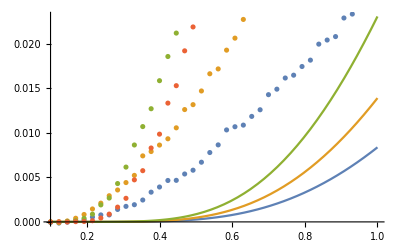

```mathematica
Show[{Plot[{Subscript[J, sub]/.{κ->1},Subscript[J, sub]/.{κ->2},Subscript[J, sub]/.{κ->5},Subscript[J, sub]/.{k->10}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v1},Transpose@{tvals,-v2},Transpose@{tvals,-v5},Transpose@{tvals,-v10}}]}]
```

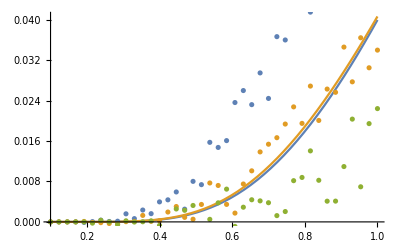

```mathematica
Show[{Plot[{Subscript[J, sub]/.{κ->30},Subscript[J, sub]/.{κ->50},Subscript[J, sub]/.{k->70}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v30},Transpose@{tvals,-v50},Transpose@{tvals,-v70}}]}]
```

```mathematica
v1t0 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k1_t0.h5","vvals"];
```

```mathematica
v2t0 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k2_t0.h5","vvals"];
```

```mathematica
v5t0 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k5_t0.h5","vvals"];
```

```mathematica
v10t0 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k10_t0.h5","vvals"];
```

```mathematica
v30t0 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k30_t0.h5","vvals"];
```

```mathematica
v50t0 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k50_t0.h5","vvals"];
```

```mathematica
v70t0 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k70_t0.h5","vvals"];
```

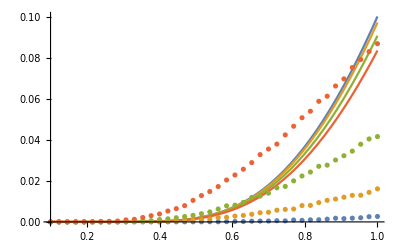

```mathematica
Show[{Plot[{Subscript[J, subz]/.{κ->1},Subscript[J, subz]/.{κ->2},Subscript[J, subz]/.{κ->5},Subscript[J, subz]/.{κ->10}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v1t0},Transpose@{tvals,-v2t0},Transpose@{tvals,-v5t0},Transpose@{tvals,-v10t0}}]}]
```

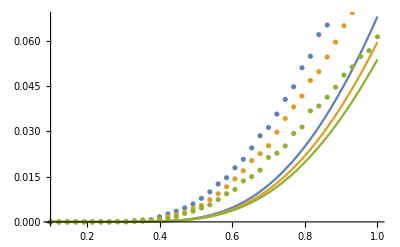

```mathematica
Show[{Plot[{Subscript[J, subz]/.{κ->30},Subscript[J, subz]/.{κ->50},Subscript[J, subz]/.{κ->70}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v30t0},Transpose@{tvals,-v50t0},Transpose@{tvals,-v70t0}}]}]
```

```mathematica
v1t001 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k1_t001.h5","vvals"];
```

```mathematica
v2t001 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k2_t001.h5","vvals"];
```

```mathematica
v5t001 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k5_t001.h5","vvals"];
```

```mathematica
v10t001 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k10_t001.h5","vvals"];
```

```mathematica
v30t001 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k30_t001.h5","vvals"];
```

```mathematica
v50t001 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k50_t001.h5","vvals"];
```

```mathematica
v70t001 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k70_t001.h5","vvals"];
```

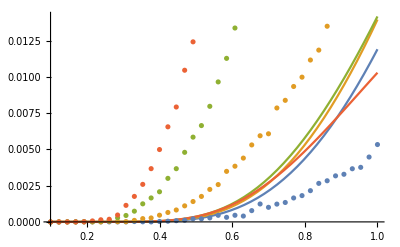

```mathematica
Show[{Plot[{Subscript[J, subr]/.{κ->1},Subscript[J, subr]/.{κ->2},Subscript[J, subr]/.{κ->5},Subscript[J, subr]/.{κ->10}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v1t001},Transpose@{tvals,-v2t001},Transpose@{tvals,-v5t001},Transpose@{tvals,-v10t001}}]}]
```

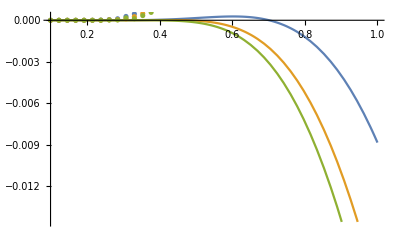

```mathematica
Show[{Plot[{Subscript[J, subr]/.{κ->30},Subscript[J, subr]/.{κ->50},Subscript[J, subr]/.{κ->70}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v30t001},Transpose@{tvals,-v50t001},Transpose@{tvals,-v70t001}}]}]
```

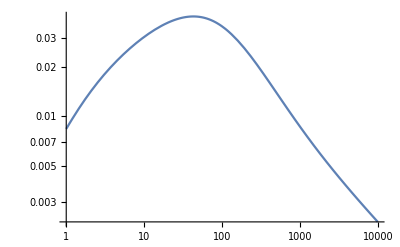

```mathematica
LogLogPlot[Subscript[J, subk],{κ,1,10000}]
```

## One-sided limit

```mathematica
Subscript[J, oneside]=FullSimplify[Limit[Subscript[J, unitless]/.{Subscript[λ, r]->(1-λ),Subscript[λ, l]->λ},{λ->0}][[1]],{κ>0,λ>0,Subscript[T, 1]>0,Subscript[T, 2]>0,Subscript[U, 0]>0}]
```

(2 ⅇ^(-4/(T_1+T_2)) κ (T_1-T_2) √((1+κ)/(κ^2 T_1^2+2 (8+κ (8+κ)) T_1 T_2+κ^2 T_2^2)) U_0)/(d^2 π γ Erf[2/(√(T_1+T_2))])

```mathematica
Subscript[J, oneexp]=FullSimplify[(Subscript[J, oneside]*d^2*γ/Subscript[U, 0])/.{Subscript[T, 2]->T-δ,Subscript[T, 1]->T+δ},{κ>0,T>0,δ>0,Subscript[U, 0]>0}]
```

(2 ⅇ^(-2/T) δ κ √((1+κ)/(-4 δ^2 (1+κ)+T^2 (2+κ)^2)))/(π Erf[(√2)/(√T)])

```mathematica
FullSimplify[Series[Subscript[J, oneexp],{δ,0,3}],{κ>0,T>0,δ>0}]
```

(2 ⅇ^(-2/T) κ √(1+κ) δ)/(π T (2+κ) Erf[(√2)/(√T)])+(4 ⅇ^(-2/T) κ (1+κ)^(3/2) δ^3)/(π T^3 (2+κ)^3 Erf[(√2)/(√T)])+O[δ]^4